```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lyliana/Documentos/Wolfram Mathematica/FIsExp

```mathematica
ExpandFileName["/home/lyliana/Documentos/Wolfram Mathematica/FIsExp"]
```

/home/lyliana/Documentos/Wolfram Mathematica/FIsExp

```mathematica
dados = Import["DadosA1.dat"];
colunas = Transpose[dados];
g1 = Transpose[{colunas[[1]],colunas[[2]]}];
g2 = Transpose[{colunas[[1]],colunas[[3]]}];
g3 = Transpose[{colunas[[1]],colunas[[4]]}];
grafico=ListPlot[{g1,g2,g3}, PlotLabel->"Intensidade luminosa em função de θ", PlotLabels->{"1.aa Medida (0±1 grau)","2.aa Medida (-20±1 grau)","3.aa Medida (-52±1 grau)"}, AxesLabel->{"θ [ °]","I"}]
```

-Graphics-

Aqui temos o ajuste puro da lei de Malus:

Lei Malus: 1.aa Medida (0±1 grau)

{A→4.33403}

{0.0361371}

0.99557

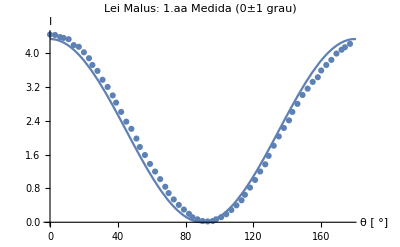

Lei Malus: 2.aa Medida (-20±1 grau)

{A→3.88818}

{0.191844}

0.864913

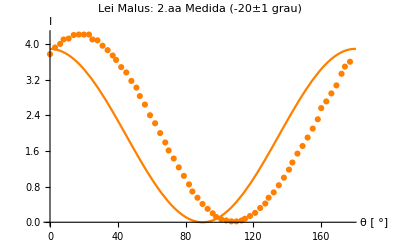

Lei Malus: 3.aa Medida (-52±1 grau)

{A→1.25822}

{0.217957}

0.335584

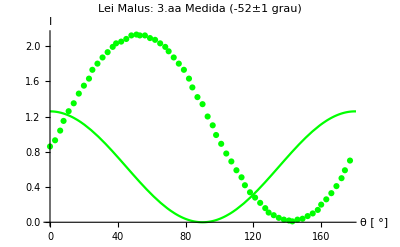

```mathematica
ferro[t_]:= A*(Cos[t Degree]^2) 
Print[ "Lei Malus: 1.aa Medida (0±1 grau)"]
ajusteg1erro = NonlinearModelFit[g1,ferro[t], {{A, 4.2}},t];
ajusteg1erro["BestFitParameters"]
ajusteg1erro["ParameterErrors"]
ajusteg1erro["AdjustedRSquared"]
Show[{ListPlot[g1],Plot[ferro[x]/.ajusteg1erro["BestFitParameters"],{x,0 ,200}]},PlotLabel-> "Lei Malus: 1.aa Medida (0±1 grau)", AxesLabel->{"θ [ °]","I"}]
Print[ "Lei Malus: 2.aa Medida (-20±1 grau)"]
ajusteg2erro = NonlinearModelFit[g2, ferro[t], {{A, 4.1}},t];
ajusteg2erro["BestFitParameters"]
ajusteg2erro["ParameterErrors"]
ajusteg2erro["AdjustedRSquared"]
Show[{  ListPlot[g2, PlotStyle->Orange],Plot[ferro[x]/.ajusteg2erro["BestFitParameters"],{x,0 ,200},  PlotStyle->Orange] }, PlotLabel-> "Lei Malus: 2.aa Medida (-20±1 grau)", AxesLabel->{"θ [ °]","I"}]
Print[ "Lei Malus: 3.aa Medida (-52±1 grau)"]
ajusteg3erro = NonlinearModelFit[g3,ferro[t], {{A, 2.}},t];
ajusteg3erro["BestFitParameters"]
ajusteg3erro["ParameterErrors"]
ajusteg3erro["AdjustedRSquared"]
Show[{ListPlot[g3, PlotStyle->Green],Plot[ferro[x]/.ajusteg3erro["BestFitParameters"],{x,0 ,200},  PlotStyle->Green] }, PlotLabel-> "Lei Malus: 3.aa Medida (-52±1 grau)", AxesLabel->{"θ [ °]","I"}]
```

Aqui são os ajustes verdadeiros, corrigindo o argumento da lei de Malus, dizendo que o teta  possui uma fase.

Lei Malus ajustada: 1.aa Medida (0±1 grau)

{A→4.34255,b→-3.13018}

{0.0116074,0.13263}

0.999543

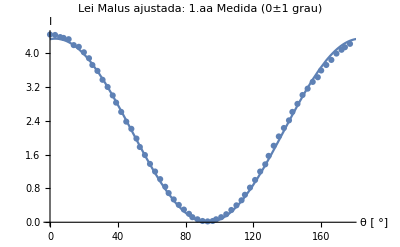

Lei Malus ajustada: 2.aa Medida (-20±1 grau)

{A→4.17535,b→-18.7337}

{0.0069846,0.0830045}

0.999821

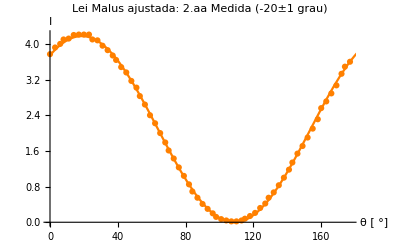

Lei Malus ajustada: 3.aa Medida (-52±1 grau)

{A→2.13892,b→128.16}

{0.00397954,0.0923192}

0.999779

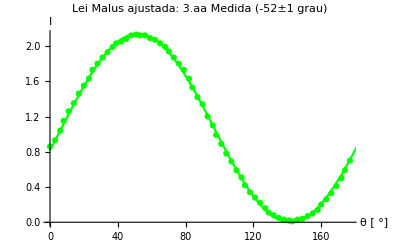

```mathematica
f[t_]:= A*(Cos[(t+ b )Degree]^2) + d
Print[ "Lei Malus ajustada: 1.aa Medida (0±1 grau)"]
ajusteg1 = NonlinearModelFit[g1,f[t], {{A, 4.2},{b,0.}},t];
ajusteg1["BestFitParameters"]
ajusteg1["ParameterErrors"]
ajusteg1["AdjustedRSquared"]
Show[{ListPlot[g1],Plot[f[x]/.ajusteg1["BestFitParameters"],{x,0 ,200}]},PlotLabel-> "Lei Malus ajustada: 1.aa Medida (0±1 grau)", AxesLabel->{"θ [ °]","I"}]
Print[ "Lei Malus ajustada: 2.aa Medida (-20±1 grau)"]
ajusteg2 = NonlinearModelFit[g2, f[t], {{A, 4.1},{b,20.}},t];
ajusteg2["BestFitParameters"]
ajusteg2["ParameterErrors"]
ajusteg2["AdjustedRSquared"]
Show[{  ListPlot[g2, PlotStyle->Orange],Plot[f[x]/.ajusteg2["BestFitParameters"],{x,0 ,200},  PlotStyle->Orange] }, PlotLabel-> "Lei Malus ajustada: 2.aa Medida (-20±1 grau)", AxesLabel->{"θ [ °]","I"}]
Print[ "Lei Malus ajustada: 3.aa Medida (-52±1 grau)"]
ajusteg3 = NonlinearModelFit[g3,f[t], {{A, 2.},{b,52.}},t];
ajusteg3["BestFitParameters"]
ajusteg3["ParameterErrors"]
ajusteg3["AdjustedRSquared"]
Show[{ListPlot[g3,  PlotStyle->Green],Plot[f[x]/.ajusteg3["BestFitParameters"],{x,0 ,200},  PlotStyle->Green] }, PlotLabel-> "Lei Malus ajustada: 3.aa Medida (-52±1 grau)", AxesLabel->{"θ [ °]","I"}]
```

```mathematica
-180+128.1601218637029890
```

-51.839878136297011

Lei Malus ajustada: 1.aa Medida (0±1 grau)

{A→4.28578,b→-3.13018,d→0.0425766}

{0.0182091,0.121717,0.0111508}

0.999625

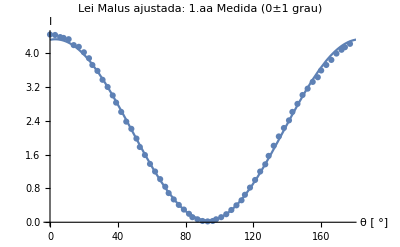

Lei Malus ajustada: 2.aa Medida (-20±1 grau)

{A→4.17605,b→-18.7337,d→-0.000525491}

{0.0121959,0.0836647,0.00746846}

0.999818

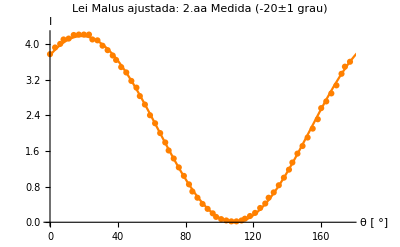

Lei Malus ajustada: 3.aa Medida (-52±1 grau)

{A→-2.13676,b→38.1601,d→2.13838}

{0.00694077,0.0930561,0.00425034}

0.999775

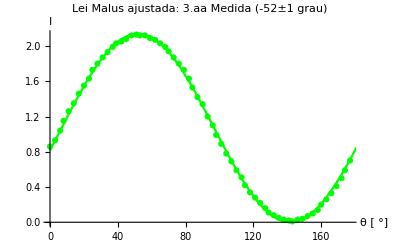

```mathematica
f[t_]:= A*(Cos[(t+ b )Degree]^2) + d
Print[ "Lei Malus ajustada: 1.aa Medida (0±1 grau)"]
ajusteg1 = NonlinearModelFit[g1,f[t], {{A, 4.2},{b,0.}, {d,0}},t];
ajusteg1["BestFitParameters"]
ajusteg1["ParameterErrors"]
ajusteg1["AdjustedRSquared"]
Show[{ListPlot[g1],Plot[f[x]/.ajusteg1["BestFitParameters"],{x,0 ,200}]},PlotLabel-> "Lei Malus ajustada: 1.aa Medida (0±1 grau)", AxesLabel->{"θ [ °]","I"}]
Print[ "Lei Malus ajustada: 2.aa Medida (-20±1 grau)"]
ajusteg2 = NonlinearModelFit[g2, f[t], {{A, 4.1},{b,20.}, {d,0}},t];
ajusteg2["BestFitParameters"]
ajusteg2["ParameterErrors"]
ajusteg2["AdjustedRSquared"]
Show[{  ListPlot[g2, PlotStyle->Orange],Plot[f[x]/.ajusteg2["BestFitParameters"],{x,0 ,200},  PlotStyle->Orange] }, PlotLabel-> "Lei Malus ajustada: 2.aa Medida (-20±1 grau)", AxesLabel->{"θ [ °]","I"}]
Print[ "Lei Malus ajustada: 3.aa Medida (-52±1 grau)"]
ajusteg3 = NonlinearModelFit[g3,f[t], {{A, 2.},{b,52.}, {d,0.}},t];
ajusteg3["BestFitParameters"]
ajusteg3["ParameterErrors"]
ajusteg3["AdjustedRSquared"]
Show[{ListPlot[g3,  PlotStyle->Green],Plot[f[x]/.ajusteg3["BestFitParameters"],{x,0 ,200},  PlotStyle->Green] }, PlotLabel-> "Lei Malus ajustada: 3.aa Medida (-52±1 grau)", AxesLabel->{"θ [ °]","I"}]
```